```mathematica
(* 2U *)
(* Defining some functions *)
a=1.7;
b=2;
c[x_,y_]=Piecewise[{{1,Abs[x]≤ 0.5 && Abs[y]≤ 0.5},{0,Abs[x]>0.5 || Abs[y]>0.5}}]; g[x_,y_]=Piecewise[{{((2^(a)-(x-y)^b))/((x+y+1)^(a)),x+y≥0&&Abs[x]≤0.5&&Abs[y]≤0.5},{((2^(a)-(x-y)^b))/(Abs[x+y-1]^(a)),x+y<0&&Abs[x]≤0.5&&Abs[y]≤0.5},{0,Abs[x]>0.5||Abs[y]>0.5}}]*c[x,y];
K[x_,y_]=g[x,y]+c[x,y]*Integrate[(Abs[t]-1)*g[t+x,-t+y],{t,-1,1}];
```

```mathematica
(* Doing some plotting of above functions *)
Plot3D[{c[x,y],g[x,y],K[x,y]},{x,-0.5,0.5},{y,-0.5,0.5},Axes->True,AxesLabel-> {x,y,z}]
```

-Graphics3D-

```mathematica
(* Computing L^2 distance of K from c *)
Sqrt[Integrate[(K[x,y]-c[x,y])^2,{x,-0.5,0.5},{y,-0.5,0.5}]]
```

0.0433182

```mathematica
(* Computing value of R(g) *)
(* Best g so far: g[x_,y_]=Piecewise[{{(4)/((x+y+1.2)^2),x+y≥0&&Abs[x]≤0.5&&Abs[y]≤0.5},{(4)/((x+y-1.2)^2),x+y<0&&Abs[x]≤0.5&&Abs[y]≤0.5},{0,Abs[x]>0.5||Abs[y]>0.5}}]*c[x,y]; gives R(g)=0.848699 and ||g-c||=0.191652 *)
Integrate[K[x,y]*g[x,y],{x,-0.5,0.5},{y,-0.5,0.5}]/(Integrate[c[x,y]*g[x,y],{x,-0.5,0.5},{y,-0.5,0.5}]);
```

```mathematica
1.0288749460715423
```

1.02887

```mathematica
0.8486986093428747
```

0.848699

```mathematica
(*************************************************************************************************************************************************************)(* 2U Separable Case *)
(* Defining some functions *)
c[x_]=Piecewise[{{1,Abs[x]≤0.5},{0,Abs[x]>0.5}}];
P[x_]=Sin[Pi*x]/(Pi*x); (* MAKE SURE TO NORMALIZE BY \Hat{P}(0)*)
h[x_]=(-1*Cos[2*Pi*x])/(2*Pi^2*x^2);
Convolve[P[t],h[t],t,x]
(*g[x_]=c[x]+(1/(2*Pi))*c[x]*Integrate[E^(2*Pi*x*u)*(Sin[Pi*u]/(Pi*u))*Convolve[P[t],h[t],t,u/(2*Pi)]/(1-Convolve[P[t],h[t],t,u/(2*Pi)]),{u,-Infinity,Infinity}]*)
```

$Aborted

```mathematica
(* Doing some plotting of above functions *)
Plot[{c[x],g[x]},{x,-0.5,0.5},Axes->True,AxesLabel-> {x,y}]
```

```mathematica
(**********************************************************************************************************************************************************)
(*(* Defining some functions *)
c[x_,y_]=Piecewise[{{1,Abs[x]≤ 0.5 && Abs[y]≤ 0.5},{0,Abs[x]>0.5 || Abs[y]>0.5}}];
f[x_,y_]=Piecewise[{{(4)/((x+y+1)^2),x+y≥0&&Abs[x]≤0.5&&Abs[y]≤0.5},{(4)/((x+y-1)^2),x+y<0&&Abs[x]≤0.5&&Abs[y]≤0.5},{0,Abs[x]>0.5||Abs[y]>0.5}}]*c[x,y];
L[x_,y_]=f[x,y]+0.25* c[x,y]*Integrate[f[x+s,y+t],{s,-1,1},{t,-1,1}]+c[x,y]*Integrate[(Abs[t]-1)*f[t+x,-t+y],{t,-1,1}]+c[x,y]*Integrate[(Abs[t]-1)*f[t+x,t+y],{t,-1,1}];
*)
```

```mathematica
(*(* Doing some plotting of above functions *)
Plot3D[{c[x,y],f[x,y],L[x,y]},{x,-0.5,0.5},{y,-0.5,0.5},Axes->True,AxesLabel-> {x,y,z}]
*)
```

```mathematica
(* Plotting image of region r under function f *)
(*ImplicitRegion[1>0,{{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5}}]
RegionPlot3D*)

r=ImplicitRegion[1>0,{{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5}}];
f[x_,y_,z_]={x-z,y,z};
RegionPlot3D[TransformedRegion[r,f],BoxRatios-> {1,1,1},Axes->True, AxesLabel->{u,v,w}]
```

-Graphics3D-

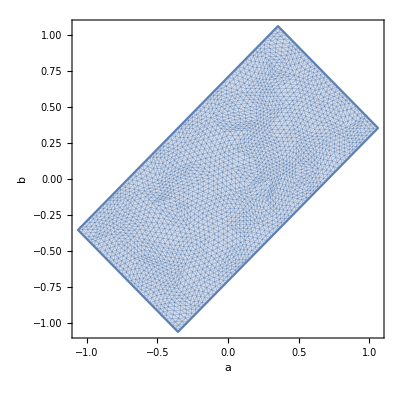

```mathematica
r=ImplicitRegion[1>0,{{x,-1,1},{y,-0.5,0.5}}];
f[x_,y_]={(x+y)/Sqrt[2],(x-y)/Sqrt[2]};
RegionPlot[TransformedRegion[r,f],Axes->True, AxesLabel->{a,b}]
```

```mathematica
(****************************************************************************************************************************************************************************************************************************************)
(* 2 U CASE BELOW *)
```

```mathematica
(* Calculations for constant h *)
(* Result for 4 terms: .511792 *)
d[x_]=Piecewise[{{1,Abs[x]≤ 0.5},{0,Abs[x]>0.5}}];
h[x_]=d[x];
K[x_]=(1-Abs[x]);

Integrate[K[x-y]*h[x-y+z]*h[z],{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5}]
Integrate[K[x-y]*K[y-z]*h[x-y+r]*h[y-z+s]*h[r]*h[s],{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5},{r,-0.5,0.5},{s,-0.5,0.5}]
Integrate[K[x-y]*K[y-z]*K[z-w]*h[x-y+r]*h[y-z+s]*h[z-w+t]*h[r]*h[s]*h[t],{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5},{w,-0.5,0.5},{r,-0.5,0.5},{s,-0.5,0.5},{t,-0.5,0.5}]
```

```mathematica
(* Calculations for h=x^2 *)
(* Result for 3 terms: .756136 *)
d[x_]=Piecewise[{{1,Abs[x]≤ 0.5},{0,Abs[x]>0.5}}];
h[x_]=x^2*d[x];
K[x_]=(1-Abs[x]);
a=1/Integrate[h[x]^2,{x,-0.5,0.5}];

a*Integrate[K[x-y]*h[x-y+z]*h[z],{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5}]
a^2*Integrate[K[x-y]*K[y-z]*h[x-y+r]*h[y-z+s]*h[r]*h[s],{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5},{r,-0.5,0.5},{s,-0.5,0.5}]
a^3*Integrate[K[x-y]*K[y-z]*K[z-w]*h[x-y+r]*h[y-z+s]*h[z-w+t]*h[r]*h[s]*h[t],{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5},{w,-0.5,0.5},{r,-0.5,0.5},{s,-0.5,0.5},{t,-0.5,0.5}]
```

```mathematica
(* Calculations for h=1-x^2 *)
(* Result for 3 terms: 0.522496 *)
d[x_]=Piecewise[{{1,Abs[x]≤ 0.5},{0,Abs[x]>0.5}}];
h[x_]=(1-x^2)*d[x];
K[x_]=(1-Abs[x]);
a=1/Integrate[h[x]^2,{x,-0.5,0.5}];

a*Integrate[K[x-y]*h[x-y+z]*h[z],{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5}]
a^2*Integrate[K[x-y]*K[y-z]*h[x-y+r]*h[y-z+s]*h[r]*h[s],{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5},{r,-0.5,0.5},{s,-0.5,0.5}]
a^3*Integrate[K[x-y]*K[y-z]*K[z-w]*h[x-y+r]*h[y-z+s]*h[z-w+t]*h[r]*h[s]*h[t],{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5},{w,-0.5,0.5},{r,-0.5,0.5},{s,-0.5,0.5},{t,-0.5,0.5}]
```

```mathematica
(* Calculations for h=1-Abs[x] *)
(* Result for *)
d[x_]=Piecewise[{{1,Abs[x]≤ 0.5},{0,Abs[x]>0.5}}];
h[x_]=(1-Abs[x])*d[x];
K[x_]=(1-Abs[x]);
a=1/Integrate[h[x]^2,{x,-0.5,0.5}];
a*Integrate[K[x-y]*h[x-y+z]*h[z],{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5}]
a^2*Integrate[K[x-y]*K[y-z]*h[x-y+r]*h[y-z+s]*h[r]*h[s],{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5},{r,-0.5,0.5},{s,-0.5,0.5}]
a^3*Integrate[K[x-y]*K[y-z]*K[z-w]*h[x-y+r]*h[y-z+s]*h[z-w+t]*h[r]*h[s]*h[t],{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5},{w,-0.5,0.5},{r,-0.5,0.5},{s,-0.5,0.5},{t,-0.5,0.5}]
```

```mathematica
(*******************************************************************************************************************************************************************************************************************************************)
(* 2 O CASE BELOW *)
```

```mathematica
(* Calculations for Constant h *)
d[x_]=Piecewise[{{1,Abs[x]≤ 0.5},{0,Abs[x]>0.5}}];
h[x_]=d[x];
a=1/Integrate[h[x]*h[x],{x,-0.5,0.5}];
b=Integrate[h[x],{x,-0.5,0.5}]^2;
K[x_,y_,t_]=0.25*b+(h[x-t+y]+h[-x+t+y])*h[y]*(1-Abs[x-t]);

a*Integrate[K[e,f,g],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5}]
a^2*Integrate[K[e,f,g]*K[g,i,j],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5}]
a^3*Integrate[K[e,f,g]*K[g,i,j]*K[j,k,l],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5},{k,-0.5,0.5},{l,-0.5,0.5}]
```

```mathematica
(* Calculations for h = x^2 *)
d[x_]=Piecewise[{{1,Abs[x]≤ 0.5},{0,Abs[x]>0.5}}];
h[x_]=x^2*d[x];
a=1/Integrate[h[x]*h[x],{x,-0.5,0.5}];
b=Integrate[h[x],{x,-0.5,0.5}]^2;
K[x_,y_,t_]=0.25*b+(h[x-t+y]+h[-x+t+y])*h[y]*(1-Abs[x-t]);

a*Integrate[K[e,f,g],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5}]
a^2*Integrate[K[e,f,g]*K[g,i,j],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5}]
a^3*Integrate[K[e,f,g]*K[g,i,j]*K[j,k,l],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5},{k,-0.5,0.5},{l,-0.5,0.5}]
```

```mathematica
(* Calculations for h = 1-x^2 *)
d[x_]=Piecewise[{{1,Abs[x]≤ 0.5},{0,Abs[x]>0.5}}];
h[x_]=(1-x^2)*d[x];
a=1/Integrate[h[x]*h[x],{x,-0.5,0.5}];
b=Integrate[h[x],{x,-0.5,0.5}]^2;
K[x_,y_,t_]=0.25*b+(h[x-t+y]+h[-x+t+y])*h[y]*(1-Abs[x-t]);

a*Integrate[K[e,f,g],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5}]
a^2*Integrate[K[e,f,g]*K[g,i,j],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5}]
a^3*Integrate[K[e,f,g]*K[g,i,j]*K[j,k,l],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5},{k,-0.5,0.5},{l,-0.5,0.5}]
```

```mathematica
(* Calculations for h = 1-Abs[x] *)
d[x_]=Piecewise[{{1,Abs[x]≤ 0.5},{0,Abs[x]>0.5}}];
h[x_]=(1-Abs[x])*d[x];
a=1/Integrate[h[x]*h[x],{x,-0.5,0.5}];
b=Integrate[h[x],{x,-0.5,0.5}]^2;
K[x_,y_,t_]=0.25*b+(h[x-t+y]+h[-x+t+y])*h[y]*(1-Abs[x-t]);

a*Integrate[K[e,f,g],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5}]
a^2*Integrate[K[e,f,g]*K[g,i,j],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5}]
a^3*Integrate[K[e,f,g]*K[g,i,j]*K[j,k,l],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5},{k,-0.5,0.5},{l,-0.5,0.5}]
```

```mathematica
(*******************************************************************************************************************************************************************************************************************************************)
(* 2 SO(E) CASE BELOW *)
```

```mathematica
(* Calculations for Constant h *)
d[x_]=Piecewise[{{1,Abs[x]≤ 0.5},{0,Abs[x]>0.5}}];
h[x_]=d[x];
c=1/Integrate[h[x],{x,-0.5,0.5}]^2;
a=1/(c*Integrate[h[x]*h[x],{x,-0.5,0.5}] + 0.5);
b=2/a;
K[x_,y_,t_]=b+c*(h[x-t+y]+h[-x+t+y])*h[y]*(Abs[x-t]-1)-c*h[y]*Integrate[h[z+y],{z,Abs[x-t]-1,1-Abs[x-t]}];

a*Integrate[K[e,f,g],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5}]
a^2*Integrate[K[e,f,g]*K[g,i,j],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5}]
a^3*Integrate[K[e,f,g]*K[g,i,j]*K[j,k,l],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5},{k,-0.5,0.5},{l,-0.5,0.5}]
```

```mathematica
(* Calculations for h = x^2 *)
d[x_]=Piecewise[{{1,Abs[x]≤ 0.5},{0,Abs[x]>0.5}}];
h[x_]=x^2*d[x];
c=1/Integrate[h[x],{x,-0.5,0.5}]^2;
a=1/(c*Integrate[h[x]*h[x],{x,-0.5,0.5}] + 0.5);
b=2/a;
K[x_,y_,t_]=b+c*(h[x-t+y]+h[-x+t+y])*h[y]*(Abs[x-t]-1)-c*h[y]*Integrate[h[z+y],{z,Abs[x-t]-1,1-Abs[x-t]}];

a*Integrate[K[e,f,g],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5}]
a^2*Integrate[K[e,f,g]*K[g,i,j],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5}]
a^3*Integrate[K[e,f,g]*K[g,i,j]*K[j,k,l],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5},{k,-0.5,0.5},{l,-0.5,0.5}]
```

```mathematica
(* Calculations for h = 1-x^2 *)
d[x_]=Piecewise[{{1,Abs[x]≤ 0.5},{0,Abs[x]>0.5}}];
h[x_]=(1-x^2)*d[x];
c=1/Integrate[h[x],{x,-0.5,0.5}]^2;
a=1/(c*Integrate[h[x]*h[x],{x,-0.5,0.5}] + 0.5);
b=2/a;
K[x_,y_,t_]=b+c*(h[x-t+y]+h[-x+t+y])*h[y]*(Abs[x-t]-1)-c*h[y]*Integrate[h[z+y],{z,Abs[x-t]-1,1-Abs[x-t]}];

a*Integrate[K[e,f,g],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5}]
a^2*Integrate[K[e,f,g]*K[g,i,j],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5}]
a^3*Integrate[K[e,f,g]*K[g,i,j]*K[j,k,l],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5},{k,-0.5,0.5},{l,-0.5,0.5}]
```

```mathematica
(* Calculations for h = 1-Abs[x] *)
d[x_]=Piecewise[{{1,Abs[x]≤ 0.5},{0,Abs[x]>0.5}}];
h[x_]=(1-Abs[x])*d[x];
c=1/Integrate[h[x],{x,-0.5,0.5}]^2;
a=1/(c*Integrate[h[x]*h[x],{x,-0.5,0.5}] + 0.5);
b=2/a;
K[x_,y_,t_]=b+c*(h[x-t+y]+h[-x+t+y])*h[y]*(Abs[x-t]-1)-c*h[y]*Integrate[h[z+y],{z,Abs[x-t]-1,1-Abs[x-t]}];

a*Integrate[K[e,f,g],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5}]
a^2*Integrate[K[e,f,g]*K[g,i,j],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5}]
a^3*Integrate[K[e,f,g]*K[g,i,j]*K[j,k,l],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5},{k,-0.5,0.5},{l,-0.5,0.5}]
```

```mathematica
(*******************************************************************************************************************************************************************************************************************************************)
(* 2 SO(O) and Sp CASES BELOW *)
```

```mathematica
(* Calculations for Constant h *)
d[x_]=Piecewise[{{1,Abs[x]≤ 0.5},{0,Abs[x]>0.5}}];
h[x_]=d[x];
c=1/Integrate[h[x],{x,-0.5,0.5}]^2;
a=1/(c*Integrate[h[x]*h[x],{x,-0.5,0.5}] + 0.5);
b=-2/a;
K[x_,y_,t_]=b+c*(h[x-t+y]+h[-x+t+y])*h[y]*(Abs[x-t]-1)+c*h[y]*Integrate[h[z+y],{z,Abs[x-t]-1,1-Abs[x-t]}];

a*Integrate[K[e,f,g],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5}]
a^2*Integrate[K[e,f,g]*K[g,i,j],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5}]
a^3*Integrate[K[e,f,g]*K[g,i,j]*K[j,k,l],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5},{k,-0.5,0.5},{l,-0.5,0.5}]
```

```mathematica
(* Calculations for h = x^2 *)
d[x_]=Piecewise[{{1,Abs[x]≤ 0.5},{0,Abs[x]>0.5}}];
h[x_]=x^2*d[x];
c=1/Integrate[h[x],{x,-0.5,0.5}]^2;
a=1/(c*Integrate[h[x]*h[x],{x,-0.5,0.5}] + 0.5);
b=-2/a;
K[x_,y_,t_]=b+c*(h[x-t+y]+h[-x+t+y])*h[y]*(Abs[x-t]-1)+c*h[y]*Integrate[h[z+y],{z,Abs[x-t]-1,1-Abs[x-t]}];

a*Integrate[K[e,f,g],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5}]
a^2*Integrate[K[e,f,g]*K[g,i,j],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5}]
a^3*Integrate[K[e,f,g]*K[g,i,j]*K[j,k,l],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5},{k,-0.5,0.5},{l,-0.5,0.5}]
```

```mathematica
(* Calculations for h = 1-x^2 *)
d[x_]=Piecewise[{{1,Abs[x]≤ 0.5},{0,Abs[x]>0.5}}];
h[x_]=(1-x^2)*d[x];
c=1/Integrate[h[x],{x,-0.5,0.5}]^2;
a=1/(c*Integrate[h[x]*h[x],{x,-0.5,0.5}] + 0.5);
b=-2/a;
K[x_,y_,t_]=b+c*(h[x-t+y]+h[-x+t+y])*h[y]*(Abs[x-t]-1)+c*h[y]*Integrate[h[z+y],{z,Abs[x-t]-1,1-Abs[x-t]}];

a*Integrate[K[e,f,g],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5}]
a^2*Integrate[K[e,f,g]*K[g,i,j],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5}]
a^3*Integrate[K[e,f,g]*K[g,i,j]*K[j,k,l],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5},{k,-0.5,0.5},{l,-0.5,0.5}]
```

```mathematica
(* Calculations for h = 1-Abs[x] *)
d[x_]=Piecewise[{{1,Abs[x]≤ 0.5},{0,Abs[x]>0.5}}];
h[x_]=(1-Abs[x])*d[x];
c=1/Integrate[h[x],{x,-0.5,0.5}]^2;
a=1/(c*Integrate[h[x]*h[x],{x,-0.5,0.5}] + 0.5);
b=-2/a;
K[x_,y_,t_]=b+c*(h[x-t+y]+h[-x+t+y])*h[y]*(Abs[x-t]-1)+c*h[y]*Integrate[h[z+y],{z,Abs[x-t]-1,1-Abs[x-t]}];

a*Integrate[K[e,f,g],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5}]
a^2*Integrate[K[e,f,g]*K[g,i,j],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5}]
a^3*Integrate[K[e,f,g]*K[g,i,j]*K[j,k,l],{e,-0.5,0.5},{f,-0.5,0.5},{g,-0.5,0.5},{i,-0.5,0.5},{j,-0.5,0.5},{k,-0.5,0.5},{l,-0.5,0.5}]
```